# Parâmetros nu - fit 2024 ( Near Detector )

## T[1][2] (T_μτ) : Plots χ^2(var) - One variable only

## 2_Reducing a list of 2 variables to 1 : { Var, Var2, χ^2 } → { Var, χ^2 }

```mathematica
Red2for1[Inlist_, Var_, Var2_]:=
Module[{tab,lis,nunN,nun3,newlisOne,list,nun,nun2,newlis,NewlisOne},
(* Código da função *)
list=Inlist;

(* Creating the list: { Var, χ^2 } *)
nun={};nun2={};
tab=Table[{list[[i,Var]],list[[i,Var2]],list[[i,3]]},{i,Length@list}];
lis=tab[[Ordering@PadRight@tab]]; 
If[Var==1,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
];
nunN=(nun-{1})/(nun2-{1});
nun2=nun2-{1};
nun3=(Length@lis)/(nunN*nun2);

newlisOne=Table[
{
 lis[[1+i*nunN[[1]],1]],
Min[ lis[[1+i*nunN[[1]]*nun2[[1]];;(1+i)*nunN[[1]],3]] ]
 }
,{i,0,nun3[[1]]-1}];


(* Return: *)
NewlisOne=newlisOne
]
```

## Without BG (9000): ϵ_μτ

### For ϵ_μτ:

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_Near9000_NSI_fit2D_WithoutBG_Eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 1, 2];
newlis

textPi = "DUNE_Near9000_NSI_fit2D_WithoutBG_PiEps_alpha";
listPi=Import[StringJoin[pathImpor,textPi]];
newlisPi=Red2for1[listPi, 1, 2];
newlisPi
```

{{0.,0.528936},{0.000015,0.108083},{0.00003,1.74546},{0.000045,5.77058},{0.00006,11.9941},{0.000075,20.3231},{0.00009,30.7101},{0.000105,43.128},{0.00012,57.5602},{0.000135,73.9957},{0.00015,92.4269},{0.000165,112.848},{0.00018,135.256},{0.000195,159.647},{0.00021,186.018},{0.000225,214.368},{0.00024,244.695},{0.000255,276.999},{0.00027,311.277},{0.000285,347.529},{0.0003,385.754}}

{{0.,0.528936},{0.000015,0.10834},{0.00003,1.74924},{0.000045,5.77755},{0.00006,12.0041},{0.000075,20.336},{0.00009,30.7258},{0.000105,43.1465},{0.00012,57.5814},{0.000135,74.0197},{0.00015,92.4537},{0.000165,112.878},{0.00018,135.288},{0.000195,159.682},{0.00021,186.056},{0.000225,214.409},{0.00024,244.739},{0.000255,277.045},{0.00027,311.325},{0.000285,347.58},{0.0003,385.808}}

0.108083

{{2}}

0.000015

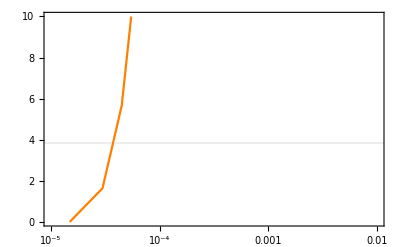

0.10834

{{2}}

0.000015

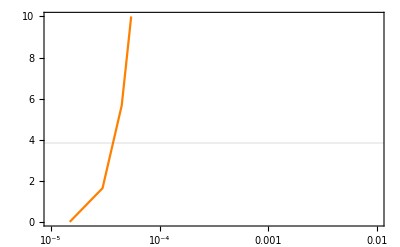

```mathematica
(* For ϵμτ positive *)
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];
min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]
(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListLogLinearPlot[DataMin, Joined->True, PlotStyle->Orange,

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]


(* For ϵμτ negative *)
dataPi = newlisPi;
xPi=Transpose[dataPi][[1]];
chi2Pi= Transpose[dataPi][[2]];
minPi=Min[chi2Pi]
posPi = Position[chi2Pi,minPi]
xminPi=xPi[[posPi[[1,1]]]]
(* Data_Plot *)
DataMinPi=Table[{xPi[[i]],chi2Pi[[i]]-minPi},{i,1,Length[xPi]}];
PlotChi2NOPi=ListLogLinearPlot[DataMinPi, Joined->True, PlotStyle->Orange,

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]


(* Without BG *)
plotWithoutBG=
Show[{PlotChi2NO},
ScalingFunctions->{"Log10",None},
PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}];
plotWithoutBGPi=
Show[{PlotChi2NOPi},
ScalingFunctions->{"Log10",None},
PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}];
```

### For α:

In this case (No BG), the term α is added only by the systematic error!

## With BG (9000): ϵ_μτ

### For ϵ_μτ:

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_Near9000_NSI_fit2D_WithBG_Eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 1, 2];
newlis

textPi = "DUNE_Near9000_NSI_fit2D_WithBG_PiEps_alpha";
listPi=Import[StringJoin[pathImpor,textPi]];
newlisPi=Red2for1[listPi, 1, 2];
newlisPi
```

{{0.,9.267×10^-9},{0.00001,0.0268892},{0.00002,0.142616},{0.00003,0.346846},{0.00004,0.637508},{0.00005,1.01388},{0.00006,1.47571},{0.00007,2.02293},{0.00008,2.65559},{0.00009,3.37382},{0.0001,4.17779},{0.00011,5.06772},{0.00012,6.04388},{0.00013,7.10655},{0.00014,8.25607},{0.00015,9.49278},{0.00016,10.8171},{0.00017,12.2294},{0.00018,13.7301},{0.00019,15.3198},{0.0002,16.9989}}

{{0.,9.341×10^-9},{0.00001,0.0269675},{0.00002,0.142825},{0.00003,0.347287},{0.00004,0.638414},{0.00005,1.01566},{0.00006,1.479},{0.00007,2.02865},{0.00008,2.66499},{0.00009,3.38852},{0.0001,4.19985},{0.00011,5.09969},{0.00012,6.08882},{0.00013,7.16811},{0.00014,8.33853},{0.00015,9.60111},{0.00016,10.957},{0.00017,12.4073},{0.00018,13.9534},{0.00019,15.5966},{0.0002,17.3384}}

9.267×10^-9

{{1}}

0.

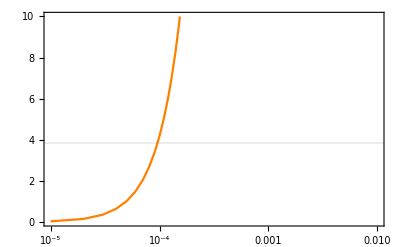

9.341×10^-9

{{1}}

0.

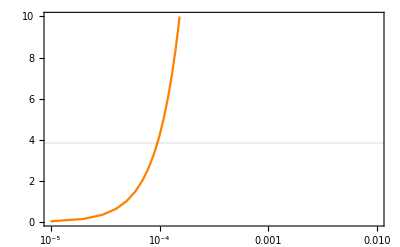

```mathematica
(* For ϵμτ positive *)
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];
min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]
(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange,
ScalingFunctions->{"Log10",None},

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]


(* For ϵμτ negative *)
dataPi = newlisPi;
xPi=Transpose[dataPi][[1]];
chi2Pi= Transpose[dataPi][[2]];
minPi=Min[chi2Pi]
posPi = Position[chi2Pi,minPi]
xminPi=xPi[[posPi[[1,1]]]]
(* Data_Plot *)
DataMinPi=Table[{xPi[[i]],chi2Pi[[i]]-minPi},{i,1,Length[xPi]}];
PlotChi2NOPi=ListPlot[DataMinPi, Joined->True, PlotStyle->Orange,
ScalingFunctions->{"Log10",None},

PlotRange->{{10^-5,10^-2},{0,10}},Frame->True,GridLines->{{},{3.84}}]
```

### For α:

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_Near8000_NSI_fit2D_WithBG_Eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 2, 1];
newlis

textPi = "DUNE_Near8000_NSI_fit2D_WithBG_PiEps_alpha";
listPi=Import[StringJoin[pathImpor,textPi]];
newlisPi=Red2for1[listPi, 2, 1];
newlisPi
```

{{-0.5,234469.15793068259},{-0.45,182957.89723481223},{-0.4,140146.11618813954},{-0.35,104397.40613722264},{-0.3,74943.5},{-0.25,51305.7},{-0.2,32781.4},{-0.15,18830.4},{-0.1,8819.45},{-0.05,2532.45},{0.,9.267×10^-9},{0.05,2562.86},{0.1,9934.72},{0.15,21687.9},{0.2,37449.4},{0.25,56891.8},{0.3,79726.4},{0.35,105697.09460196989},{0.4,134575.70724913865},{0.45,166158.14146721541},{0.5,200261.0490954977}}

{{-0.5,234468.97333452659},{-0.45,182957.70626585238},{-0.4,140145.92597406724},{-0.35,104397.37718845585},{-0.3,74943.5},{-0.25,51305.7},{-0.2,32781.4},{-0.15,18830.4},{-0.1,8819.42},{-0.05,2532.44},{0.,9.267×10^-9},{0.05,2562.86},{0.1,9934.72},{0.15,21687.9},{0.2,37449.4},{0.25,56891.8},{0.3,79726.4},{0.35,105697.09460196989},{0.4,134575.70724913865},{0.45,166158.14146721541},{0.5,200261.0490954977}}

9.267×10^-9

{{11}}

0.

9.267×10^-9

{{11}}

0.

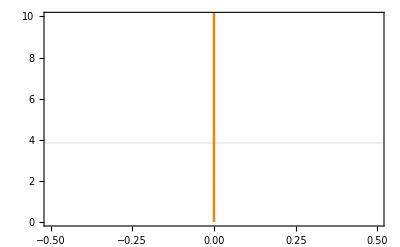

-Graphics-

```mathematica
(* For ϵμτ positive *)
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];
min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]
(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* For ϵμτ negative *)
dataPi = newlisPi;
xPi=Transpose[dataPi][[1]];
chi2Pi= Transpose[dataPi][[2]];
minPi=Min[chi2Pi]
posPi = Position[chi2Pi,minPi]
xminPi=xPi[[posPi[[1,1]]]]
(* Data_Plot *)
DataMinPi=Table[{xPi[[i]],chi2Pi[[i]]-minPi},{i,1,Length[xPi]}];
PlotChi2NOPi=ListPlot[DataMinPi, Joined->True, PlotStyle->Orange];


(* With BG *)
plotWithoutBG=
Show[{PlotChi2NO},PlotRange->{0,10},Frame->True,GridLines->{{},{3.84}}]
plotWithoutBGPi=
Show[{PlotChi2NOPi},PlotRange->{0,10},Frame->True,GridLines->{{},{3.84}}]
```

# Antigo: parâmetros do artigo e não do nu - fit 2024 (não tem mais os arquivos)

## T[1][2] (T_μτ) : Plots χ^2(var) - One variable only

#### 2_Reducing a list of 2 variables to 1 : { Var, Var2, χ^2 } → { Var, χ^2 }

```mathematica
Red2for1[Inlist_, Var_, Var2_]:=
Module[{tab,lis,nunN,nun3,newlisOne,list,nun,nun2,newlis,NewlisOne},
(* Código da função *)
list=Inlist;

(* Creating the list: { Var, χ^2 } *)
nun={};nun2={};
tab=Table[{list[[i,Var]],list[[i,Var2]],list[[i,3]]},{i,Length@list}];
lis=tab[[Ordering@PadRight@tab]]; 
If[Var==1,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
];
nunN=(nun-{1})/(nun2-{1});
nun2=nun2-{1};
nun3=(Length@lis)/(nunN*nun2);

newlisOne=Table[
{
 lis[[1+i*nunN[[1]],1]],
Min[ lis[[1+i*nunN[[1]]*nun2[[1]];;(1+i)*nunN[[1]],3]] ]
 }
,{i,0,nun3[[1]]-1}];


(* Return: *)
NewlisOne=newlisOne
]
```

#### 3_Type - 1a : ϵ_μτ

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_NSI_fit2D_eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 1, 2];
newlis

textBG = "DUNE_NSI_fit2D_BG_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG, 1, 2];
newlisBG
```

{{-0.02,97.4686},{-0.018,66.9759},{-0.016,43.4369},{-0.014,26.1349},{-0.012,14.2283},{-0.01,6.75496},{-0.008,2.65317},{-0.006,0.820599},{-0.004,0.224584},{-0.002,0.069282},{0.,0.},{0.002,0.250498},{0.004,1.62595},{0.006,5.3147},{0.008,12.6424},{0.01,24.8827},{0.012,43.1547},{0.014,68.3934},{0.016,101.353},{0.018,142.626},{0.02,192.671}}

{{-0.02,89.9265},{-0.018,61.5855},{-0.016,39.8043},{-0.014,23.9194},{-0.012,12.908},{-0.01,6.04148},{-0.008,2.39015},{-0.006,0.682851},{-0.004,0.141326},{-0.002,0.0418864},{0.,0.},{0.002,0.205615},{0.004,1.27029},{0.006,4.09334},{0.008,9.9957},{0.01,20.1875},{0.012,35.5122},{0.014,57.06},{0.016,85.6268},{0.018,121.822},{0.02,166.123}}

##### Without_BG

0.

{{11}}

0.

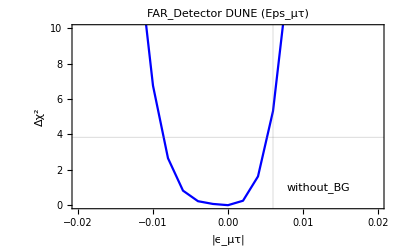

```mathematica
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Blue];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* Without BG *)
plot=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["|ϵ_μτ|",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["without_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{0.006},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### With_BG

0.

{{11}}

0.

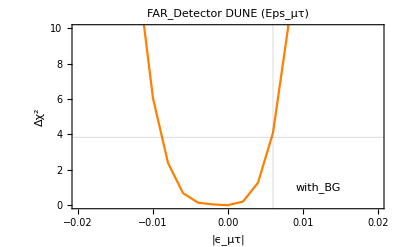

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["|ϵ_μτ|",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{0.006},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

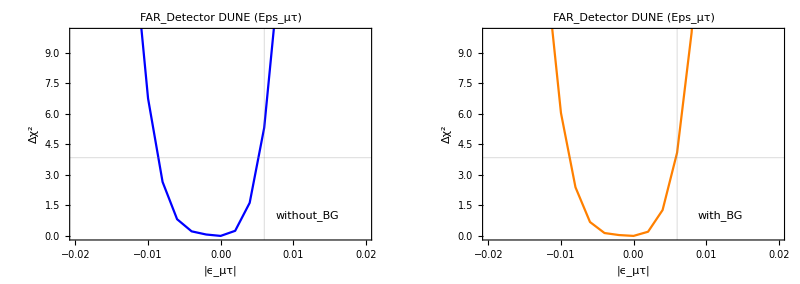

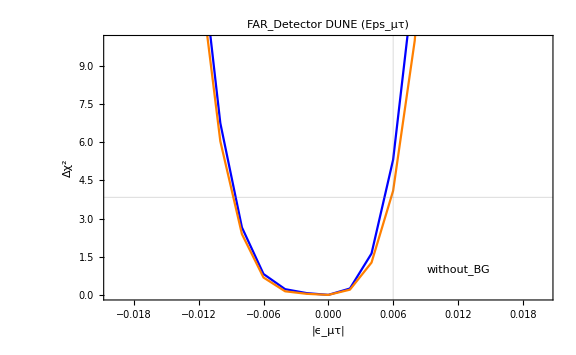

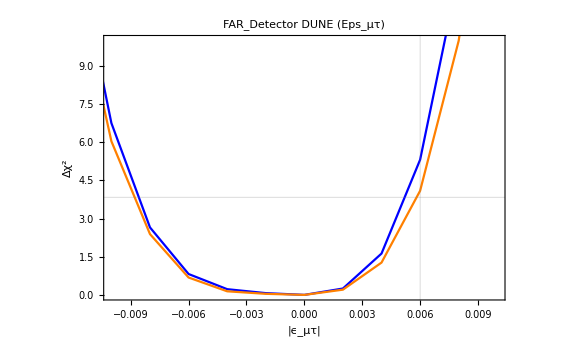

```mathematica
GraphicsRow[{plot,plotBG}]
Show[plot,plotBG,ImageSize->Large]
Show[plot,plotBG,PlotRange->{{-0.01,0.01},{0,10}},ImageSize->Large]
```

#### 3_Type - 1b : α

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_02_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];
text = "DUNE_NSI_fit2D_eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list,2, 1];
newlis

textBG = "DUNE_NSI_fit2D_BG_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG,2, 1];
newlisBG
```

{{-0.5,20.},{-0.45,16.2},{-0.4,12.8},{-0.35,9.8},{-0.3,7.2},{-0.25,5.},{-0.2,3.2},{-0.15,1.8},{-0.1,0.8},{-0.05,0.2},{0.,0.},{0.05,0.2},{0.1,0.8},{0.15,1.8},{0.2,3.2},{0.25,5.},{0.3,7.2},{0.35,9.8},{0.4,12.8},{0.45,16.2},{0.5,20.}}

{{-0.5,53.655},{-0.45,42.3566},{-0.4,32.4984},{-0.35,24.3179},{-0.3,17.677},{-0.25,11.9436},{-0.2,7.46182},{-0.15,4.23572},{-0.1,1.81532},{-0.05,0.473557},{0.,0.},{0.05,0.46523},{0.1,1.88231},{0.15,4.25342},{0.2,7.54303},{0.25,11.7192},{0.3,16.753},{0.35,22.6183},{0.4,29.2912},{0.45,36.7501},{0.5,44.975}}

##### Without_BG

0.

{{11}}

0.

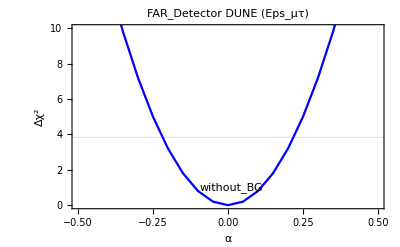

```mathematica
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Blue];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* Without BG *)
plot=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["α",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["without_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### With_BG

0.

{{11}}

0.

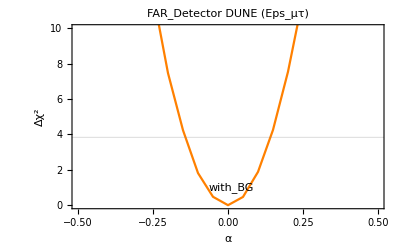

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["α",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

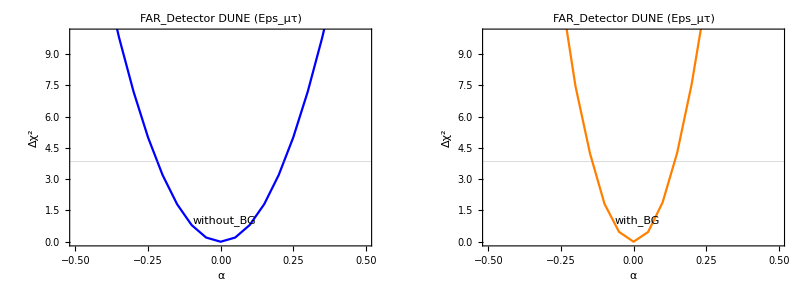

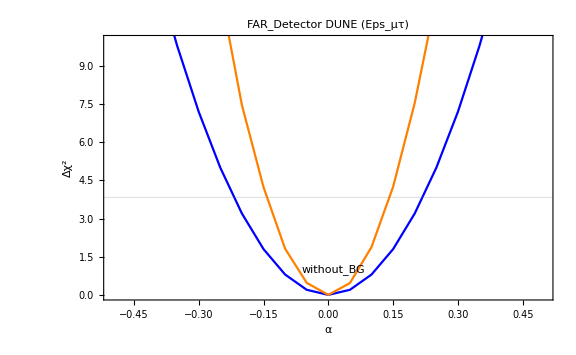

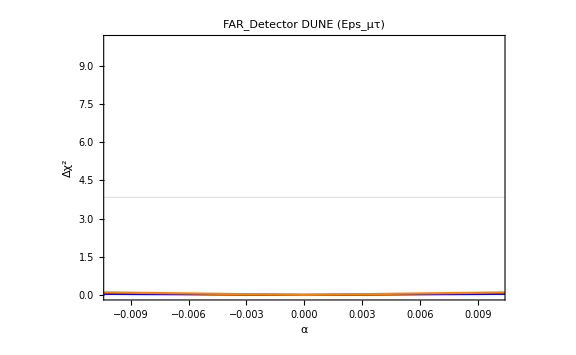

```mathematica
GraphicsRow[{plot,plotBG}]
Show[plot,plotBG,ImageSize->Large]
Show[plot,plotBG,PlotRange->{{-0.01,0.01},{0,10}},ImageSize->Large]
```

#### 3_Type - 2a : ϵ_μτ

```mathematica
pathImpor=NotebookDirectory[];

textBG = "DUNE_NSI_fit2D_BG2_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG, 1, 2];
newlisBG
```

{{-0.02,89.9265},{-0.019,74.8987},{-0.018,61.5855},{-0.017,49.9139},{-0.016,39.8043},{-0.015,31.1256},{-0.014,23.8066},{-0.013,17.7647},{-0.012,12.8962},{-0.011,9.00299},{-0.01,6.04148},{-0.009,3.85963},{-0.008,2.31167},{-0.007,1.28852},{-0.006,0.682851},{-0.005,0.313176},{-0.004,0.141326},{-0.003,0.0729667},{-0.002,0.0418864},{-0.001,0.0160465},{0.,0.},{0.001,0.0366642},{0.002,0.205615},{0.003,0.528411},{0.004,1.21166},{0.005,2.34459},{0.006,4.09334},{0.007,6.57513},{0.008,9.9957},{0.009,14.4408},{0.01,20.0691},{0.011,27.0348},{0.012,35.4532},{0.013,45.4347},{0.014,57.06},{0.015,70.4247},{0.016,85.6268},{0.017,102.738},{0.018,121.822},{0.019,142.934},{0.02,166.123}}

##### With_BG

0.

{{21}}

0.

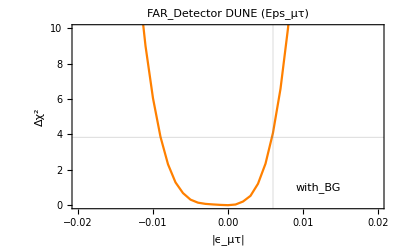

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["|ϵ_μτ|",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{0.006},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

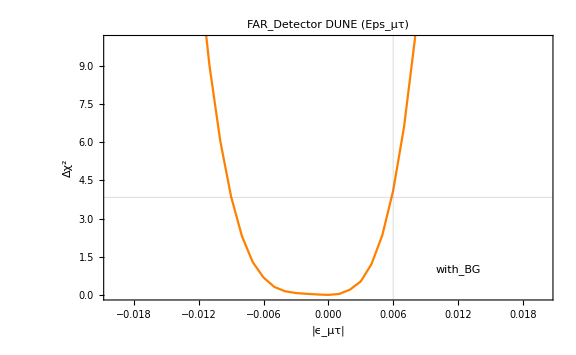

```mathematica
Show[plotBG,ImageSize->Large]
```

#### 3_Type - 2b : α

```mathematica
pathImpor=NotebookDirectory[];

textBG = "DUNE_NSI_fit2D_BG2_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG,2, 1];
newlisBG
```

{{-0.5,53.4784},{-0.475,47.5774},{-0.45,42.159},{-0.425,37.1989},{-0.4,32.4984},{-0.375,28.2077},{-0.35,24.3179},{-0.325,20.7662},{-0.3,17.4683},{-0.275,14.5279},{-0.25,11.9324},{-0.225,9.54079},{-0.2,7.46182},{-0.175,5.69659},{-0.15,4.12605},{-0.125,2.84378},{-0.1,1.81532},{-0.075,1.0069},{-0.05,0.452638},{-0.025,0.11315},{0.,0.},{0.025,0.111977},{0.05,0.460938},{0.075,1.05214},{0.1,1.88231},{0.125,2.95092},{0.15,4.25342},{0.175,5.78549},{0.2,7.54303},{0.225,9.52216},{0.25,11.7192},{0.275,14.1306},{0.3,16.753},{0.325,19.5832},{0.35,22.6183},{0.375,25.8552},{0.4,29.2912},{0.425,32.9237},{0.45,36.7501},{0.475,40.768},{0.5,44.975}}

##### With_BG

0.

{{21}}

0.

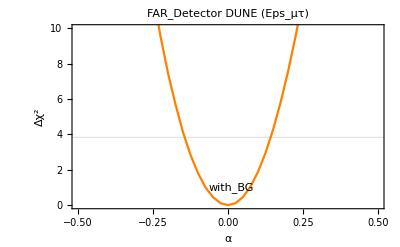

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["α",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"FAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

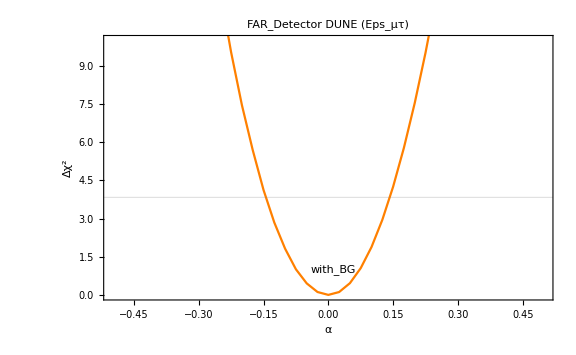

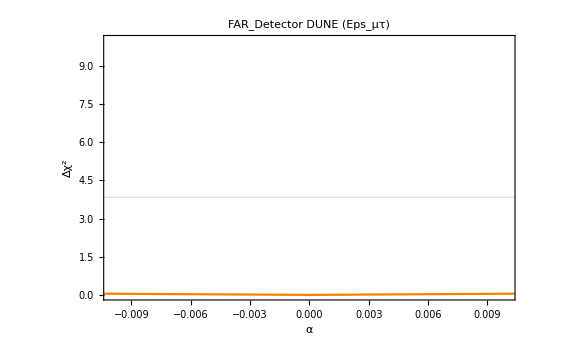

```mathematica
Show[plotBG,ImageSize->Large]
Show[plotBG,PlotRange->{{-0.01,0.01},{0,10}},ImageSize->Large]
```